```mathematica
Get[FileNameJoin[{NotebookDirectory[], "functions.m"}]]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
buses = {b1, b3, b11, b12, b13, b15, b17, b18, b19, b20, b23};
routeNames = {"1", "3", "11", "12", "13", "15", "17", "18", "19", "20", "23"};
```

```mathematica
TAPs=Algorithm821[buses, routeNames, Quantity[16, "Minutes"]];
```

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

```mathematica
mtx =ImportMaxPlustMatrix["matrix138"];
```

```mathematica
Dimensions[mtx]
```

{244,244}

```mathematica
Count[#[[2]]&/@Values[TAPs[[3]]], 0]
```

126

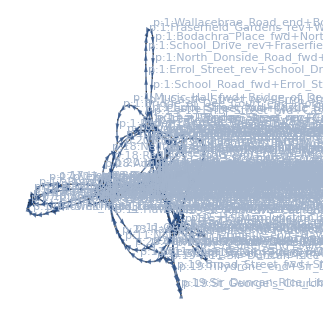

```mathematica
CreatePetriNetFromTAPs[TAPs]
```

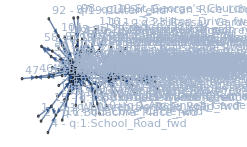

```mathematica
MakeAdjacencyGraph[mtx, TAPs]
```

```mathematica
mtx // MatrixForm
```

```mathematica
TimeObject[{0,#,0}] &/@ xnext
```

{00:57:00TimeObject[{0,57,0.},Instant],01:05:00TimeObject[{1,5,0.},Instant],01:14:00TimeObject[{1,14,0.},Instant],01:25:00TimeObject[{1,25,0.},Instant],01:37:00TimeObject[{1,37,0.},Instant],01:45:00TimeObject[{1,45,0.},Instant],01:53:00TimeObject[{1,53,0.},Instant],00:34:00TimeObject[{0,34,0.},Instant],00:45:00TimeObject[{0,45,0.},Instant],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],00:16:00TimeObject[{0,16,0.},Instant],00:25:00TimeObject[{0,25,0.},Instant],00:34:00TimeObject[{0,34,0.},Instant],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],00:15:00TimeObject[{0,15,1.13687×10^-13},Instant],00:22:00TimeObject[{0,22,0.},Instant],00:33:00TimeObject[{0,33,0.},Instant],00:44:00TimeObject[{0,44,0.},Instant]}

```mathematica
v = MakeStateVector[mtx]
```

{-∞,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,-∞,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,-∞,-∞,0,-∞,0,-∞,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,0,0,-∞,0,-∞,0}

```mathematica
v={0, 0,0,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,4,-∞,0,2,0, 0,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,5,-∞,0,-∞,0,-∞,-∞,0,0,5,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,3,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,12,0,0,-∞,0,-∞,0}
```

{0,0,0,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,4,-∞,0,2,0,0,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,5,-∞,0,-∞,0,-∞,-∞,0,0,5,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,3,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,12,0,0,-∞,0,-∞,0}

```mathematica
mtx = ImportMaxPlustMatrix["matrix_no2_ct15"]
```

```mathematica
TimeTable[mtx_, vec_, transitions_] := Module[{xNext, list, kpx},
	kpx = Association[1 -> mtx];
	list = List[vec];
	i = 2;
	xNext = mtimes[mpower[mtx, 1], vec];
	AppendTo[list, xNext];
	While[i< 12,
		powerAndKnown = mpowerDynamic[mtx, i, kpx];
           Print[i];
		xNext = mtimes[powerAndKnown[[1]], vec];
		kpx = powerAndKnown[[2]];
		AppendTo[list, xNext];
		i++;
];
	Join[{transitions}, list]
]
```

```mathematica
ttb = TimeTable[mtx,v, TAPs[[1]]];
```

2

3

4

5

6

7

8

9

10

11

```mathematica
ttb
```

{{q:1:Wallacebrae_Road_end,q:1:Bodachra_Place_fwd,q:1:North_Donside_Road_fwd,q:1:School_Road_fwd,q:1:Errol_Street_fwd,q:1:Castle_Street_fwd,q:1:Music_Hall_fwd,q:1:Bridge_of_Dee_Court_end,q:1:Robert_Gordon_University_rev,q:1:Auchinyell_Gardens_rev,q:1:Great_Western_Road_rev,q:1:Castle_Street_rev,q:1:Errol_Street_rev,q:1:School_Drive_rev,q:1:Fraserfield_Gardens_rev,q:3:Cove_Circle_end,q:3:Altens_Farm_Road_fwd,q:3:Victoria_Bridge_fwd,q:3:Guild_Street_fwd,q:3:Gilcomston_Park_fwd,q:3:ARI_Bus_Port_fwd,q:3:Mastrick_end,q:3:Aberdeen_Royal_Infirmary_rev,q:3:Bridge_Street_rev,q:3:Guild_Street_rev,q:3:Altens_Farm_Road_rev,q:11:Northfield_Terminus_end,q:11:Hawthorn_Crescent_fwd,q:11:Berryden_Retail_Park_fwd,q:11:Adelphi_fwd,q:11:Queen's_Cross_fwd,q:11:Woodend_end,q:11:Queen's_Cross_rev,q:11:Broad_Street_rev,q:11:Berryden_Retail_Park_rev,q:12:Heathryfold_end,q:12:Belmont_Road_fwd,q:12:Bridge_Street_fwd,q:12:Guild_Street_fwd,q:12:Torry_Terminus_end,q:12:Guild_Street_rev,q:12:Chestnut_Row_rev,q:13:Golf_Links_end,q:13:Beach_Boulevard_fwd,q:13:St_Andrew's_Cathedral_fwd,q:13:Prince_Arthur_Street_fwd,q:13:Mastrick_Shops_fwd,q:13:Turning_Circle_end,q:13:Summerhill_Terrace_rev,q:13:Bridge_Street_rev,q:13:Castle_Street_rev,q:13:Beach_Boulevard_rev,q:15:Balnagask_Circle_end,q:15:Victoria_Bridge_fwd,q:15:Guild_Street_fwd,q:15:Holburn_Junction_fwd,q:15:Pinewood_Place_fwd,q:15:North_Countesswells_Road_fwd,q:15:Countesswells_Park_Road_end,q:15:Airyhall_rev,q:15:Holburn_Junction_rev,q:15:Guild_Street_rev,q:17:Dyce_end,q:17:Riverview_Drive_fwd,q:17:Newhills_fwd,q:17:Howes_Road_fwd,q:17:Mugiemoss_Road_fwd,q:17:Millbank_Place_fwd,q:17:Bon_Accord_Centre_fwd,q:17:Adelphi_fwd,q:17:Abbotswell_School_fwd,q:17:Faulds_Gate_end,q:17:Devanha_Gardens_rev,q:17:Adelphi_rev,q:17:Bon_Accord_Centre_rev,q:17:Millbank_Place_rev,q:17:Smithfield_Lane_rev,q:17:Howes_Road_rev,q:17:Cloverfield_Gardens_rev,q:18:Dyce_end,q:18:Riverview_Drive_fwd,q:18:Mugiemoss_Road_fwd,q:18:Powis_Lane_fwd,q:18:Adelphi_fwd,q:18:Nellfield_Place_fwd,q:18:Redmoss_Road_end,q:18:Great_Western_Road_rev,q:18:Adelphi_rev,q:18:Calsayseat_Road_rev,q:18:Smithfield_Lane_rev,q:18:Riverview_Drive_rev,q:19:Culter_end,q:19:Milton_of_Murtle_fwd,q:19:Mannofield_Church_fwd,q:19:Holburn_Junction_fwd,q:19:Broad_Street_fwd,q:19:Sir_Duncan_Rice_Library_fwd,q:19:St_George's_Church_fwd,q:19:Tillydrone_end,q:19:Sir_Duncan_Rice_Library_rev,q:19:Broad_Street_rev,q:19:Holburn_Junction_rev,q:19:Mannofield_Church_rev,q:19:Cairn_Road_rev,q:20:Guild_Street_end,q:20:Castle_Street_fwd,q:20:Kings_College_fwd,q:20:Hillhead_Of_Seaton_end,q:20:Kings_College_rev,q:20:Adelphi_rev,q:23:Raasay_Gardens_end,q:23:Raeden_Avenue_fwd,q:23:Carden_Place_fwd,q:23:Adelphi_fwd,q:23:Fraser_Place_fwd,q:23:Hilton_Drive_fwd,q:23:Heathryfold_end,q:23:Hilton_Drive_rev,q:23:St_Andrew's_Cathedral_rev,q:23:Holburn_Junction_rev,q:23:Harcourt_Road_rev,q:23:Colonsay_Crescent_rev},{-∞,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,-∞,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,-∞,-∞,0,-∞,0,-∞,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,0,0,-∞,0,-∞,0},{13.,20.,27.,7.,12.,38.,43.,14.,18.,8.,23.,38.,42.,5.,12.,9.,19.,25.,32.,6.,17.,10.,9.,19.,32.,9.,23.,31.,9.,21.,12.,8.,16.,15.,11.,24.,36.,19.,32.,10.,32.,14.,14.,24.,14.,13.,15.,24.,15.,19.,38.,44.,14.,25.,30.,41.,15.,15.,6.,15.,23.,32.,17.,28.,36.,10.,17.,10.,6.,21.,13.,19.,11.,21.,25.,29.,16.,22.,8.,17.,28.,17.,10.,21.,10.,11.,23.,21.,7.,16.,21.,13.,27.,15.,41.,10.,14.,17.,20.,8.,15.,41.,11.,22.,32.,38.,9.,17.,9.,21.,4.,14.,9.,21.,7.,9.,24.,11.,14.,41.,9.,17.},{25.,32.,39.,34.,39.,68.,73.,57.,61.,26.,34.,68.,72.,47.,54.,18.,28.,57.,62.,38.,49.,27.,19.,46.,52.,41.,38.,46.,40.,51.,33.,20.,28.,50.,26.,56.,68.,46.,62.,42.,62.,46.,58.,68.,34.,27.,28.,37.,39.,46.,68.,74.,46.,57.,62.,73.,56.,30.,21.,21.,43.,62.,39.,50.,58.,46.,53.,27.,16.,51.,34.,40.,30.,51.,55.,59.,37.,43.,30.,39.,50.,53.,27.,51.,31.,21.,34.,51.,28.,37.,43.,35.,49.,42.,73.,50.,24.,27.,30.,28.,26.,73.,52.,63.,62.,68.,47.,55.,26.,51.,21.,31.,23.,51.,28.,16.,56.,35.,34.,73.,50.,58.},{67.,74.,81.,46.,51.,102.,107.,87.,91.,69.,77.,102.,106.,77.,84.,50.,60.,87.,96.,68.,79.,59.,36.,78.,96.,61.,73.,81.,55.,76.,63.,41.,49.,82.,61.,86.,98.,78.,96.,72.,96.,76.,88.,98.,78.,47.,42.,51.,52.,78.,102.,108.,76.,87.,92.,103.,88.,71.,36.,36.,87.,96.,60.,71.,79.,68.,75.,63.,33.,76.,64.,70.,51.,76.,80.,84.,67.,73.,51.,60.,71.,75.,63.,76.,61.,42.,77.,76.,58.,67.,64.,76.,90.,64.,103.,82.,64.,67.,70.,38.,43.,103.,84.,95.,96.,102.,77.,85.,64.,76.,62.,72.,40.,76.,58.,37.,86.,67.,78.,103.,82.,90.},{97.,104.,111.,88.,93.,132.,137.,121.,125.,99.,107.,132.,136.,111.,118.,70.,80.,121.,126.,102.,113.,89.,68.,108.,126.,105.,105.,113.,90.,106.,88.,71.,79.,112.,93.,120.,132.,108.,126.,106.,126.,110.,122.,132.,108.,91.,62.,71.,66.,108.,132.,138.,110.,121.,126.,137.,118.,103.,77.,51.,117.,126.,90.,101.,109.,89.,96.,85.,69.,106.,89.,95.,81.,106.,110.,114.,92.,98.,81.,90.,101.,96.,85.,106.,86.,72.,107.,106.,83.,92.,94.,108.,122.,105.,137.,112.,96.,99.,102.,78.,59.,137.,114.,125.,126.,132.,111.,119.,94.,106.,94.,104.,81.,106.,83.,67.,120.,97.,108.,137.,112.,120.},{131.,138.,145.,118.,123.,166.,171.,151.,155.,133.,141.,166.,170.,141.,148.,114.,124.,151.,160.,132.,143.,123.,98.,142.,160.,135.,135.,143.,122.,140.,118.,96.,104.,146.,123.,150.,162.,142.,160.,136.,160.,140.,152.,162.,142.,121.,106.,115.,86.,142.,166.,172.,140.,151.,156.,167.,152.,133.,109.,92.,151.,160.,115.,126.,134.,119.,126.,106.,91.,140.,119.,125.,106.,140.,144.,148.,122.,128.,106.,115.,126.,126.,106.,140.,116.,97.,141.,140.,113.,122.,119.,138.,152.,137.,167.,146.,126.,129.,132.,110.,93.,167.,148.,159.,160.,166.,141.,149.,128.,140.,124.,134.,113.,140.,113.,92.,150.,131.,142.,167.,146.,154.},{161.,168.,175.,152.,157.,196.,201.,185.,189.,163.,171.,196.,200.,175.,182.,144.,154.,185.,190.,166.,177.,153.,132.,172.,190.,169.,169.,177.,152.,170.,152.,126.,134.,176.,157.,184.,196.,172.,190.,170.,190.,174.,186.,196.,172.,155.,136.,145.,130.,172.,196.,202.,174.,185.,190.,201.,182.,167.,139.,124.,181.,190.,145.,156.,164.,144.,151.,136.,112.,170.,153.,159.,136.,170.,174.,178.,156.,162.,136.,145.,156.,151.,136.,170.,150.,127.,171.,170.,147.,156.,149.,172.,186.,167.,201.,176.,160.,163.,166.,140.,125.,201.,178.,189.,190.,196.,175.,183.,158.,170.,158.,168.,143.,170.,147.,122.,184.,161.,172.,201.,176.,184.},{195.,202.,209.,182.,187.,230.,235.,215.,219.,197.,205.,230.,234.,205.,212.,178.,188.,215.,224.,196.,207.,187.,162.,206.,224.,199.,199.,207.,186.,204.,182.,160.,168.,210.,187.,214.,226.,206.,224.,200.,224.,204.,216.,226.,206.,185.,170.,179.,160.,206.,230.,236.,204.,215.,220.,231.,216.,197.,173.,154.,215.,224.,179.,190.,198.,174.,181.,161.,142.,204.,183.,189.,170.,204.,208.,212.,186.,192.,170.,179.,190.,181.,161.,204.,180.,161.,205.,204.,177.,186.,183.,202.,216.,201.,231.,210.,190.,193.,196.,174.,155.,231.,212.,223.,224.,230.,205.,213.,192.,204.,188.,198.,177.,204.,177.,156.,214.,195.,206.,231.,210.,218.},{225.,232.,239.,216.,221.,260.,265.,249.,253.,227.,235.,260.,264.,239.,246.,208.,218.,249.,254.,230.,241.,217.,196.,236.,254.,233.,233.,241.,216.,234.,216.,190.,198.,240.,221.,248.,260.,236.,254.,234.,254.,238.,250.,260.,236.,219.,200.,209.,194.,236.,260.,266.,238.,249.,254.,265.,246.,231.,203.,188.,245.,254.,209.,220.,228.,208.,215.,191.,167.,234.,217.,223.,200.,234.,238.,242.,220.,226.,200.,209.,220.,215.,191.,234.,214.,191.,235.,234.,211.,220.,213.,236.,250.,231.,265.,240.,224.,227.,230.,204.,189.,265.,242.,253.,254.,260.,239.,247.,222.,234.,222.,232.,207.,234.,211.,186.,248.,225.,236.,265.,240.,248.},{259.,266.,273.,246.,251.,294.,299.,279.,283.,261.,269.,294.,298.,269.,276.,242.,252.,279.,288.,260.,271.,251.,226.,270.,288.,263.,263.,271.,250.,268.,246.,224.,232.,274.,251.,278.,290.,270.,288.,264.,288.,268.,280.,290.,270.,249.,234.,243.,224.,270.,294.,300.,268.,279.,284.,295.,280.,261.,237.,218.,279.,288.,243.,254.,262.,238.,245.,225.,197.,268.,247.,253.,234.,268.,272.,276.,250.,256.,234.,243.,254.,245.,225.,268.,244.,225.,269.,268.,241.,250.,247.,266.,280.,265.,295.,274.,254.,257.,260.,238.,219.,295.,276.,287.,288.,294.,269.,277.,256.,268.,252.,262.,241.,268.,241.,220.,278.,259.,270.,295.,274.,282.},{289.,296.,303.,280.,285.,324.,329.,313.,317.,291.,299.,324.,328.,303.,310.,272.,282.,313.,318.,294.,305.,281.,260.,300.,318.,297.,297.,305.,280.,298.,280.,254.,262.,304.,285.,312.,324.,300.,318.,298.,318.,302.,314.,324.,300.,283.,264.,273.,258.,300.,324.,330.,302.,313.,318.,329.,310.,295.,267.,252.,309.,318.,273.,284.,292.,272.,279.,255.,231.,298.,281.,287.,264.,298.,302.,306.,284.,290.,264.,273.,284.,279.,255.,298.,278.,255.,299.,298.,275.,284.,277.,300.,314.,295.,329.,304.,288.,291.,294.,268.,253.,329.,306.,317.,318.,324.,303.,311.,286.,298.,286.,296.,271.,298.,275.,250.,312.,289.,300.,329.,304.,312.},{323.,330.,337.,310.,315.,358.,363.,343.,347.,325.,333.,358.,362.,333.,340.,306.,316.,343.,352.,324.,335.,315.,290.,334.,352.,327.,327.,335.,314.,332.,310.,288.,296.,338.,315.,342.,354.,334.,352.,328.,352.,332.,344.,354.,334.,313.,298.,307.,288.,334.,358.,364.,332.,343.,348.,359.,344.,325.,301.,282.,343.,352.,307.,318.,326.,302.,309.,289.,261.,332.,311.,317.,298.,332.,336.,340.,314.,320.,298.,307.,318.,309.,289.,332.,308.,289.,333.,332.,305.,314.,311.,330.,344.,329.,359.,338.,318.,321.,324.,302.,283.,359.,340.,351.,352.,358.,333.,341.,320.,332.,316.,326.,305.,332.,305.,284.,342.,323.,334.,359.,338.,346.}}

```mathematica
ttb // Transpose // MatrixForm
```

(q:1:Wallacebrae_Road_end | 0 | 13. | 25. | 67. | 97. | 131. | 161. | 195. | 225. | 259. | 289. | 323.
q:1:Bodachra_Place_fwd | 0 | 20. | 32. | 74. | 104. | 138. | 168. | 202. | 232. | 266. | 296. | 330.
q:1:North_Donside_Road_fwd | 0 | 27. | 39. | 81. | 111. | 145. | 175. | 209. | 239. | 273. | 303. | 337.
q:1:School_Road_fwd | 0 | 7. | 34. | 46. | 88. | 118. | 152. | 182. | 216. | 246. | 280. | 310.
q:1:Errol_Street_fwd | 0 | 12. | 39. | 51. | 93. | 123. | 157. | 187. | 221. | 251. | 285. | 315.
q:1:Castle_Street_fwd | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324. | 358.
q:1:Music_Hall_fwd | 0 | 43. | 73. | 107. | 137. | 171. | 201. | 235. | 265. | 299. | 329. | 363.
q:1:Bridge_of_Dee_Court_end | -∞ | 14. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279. | 313. | 343.
q:1:Robert_Gordon_University_rev | 0 | 18. | 61. | 91. | 125. | 155. | 189. | 219. | 253. | 283. | 317. | 347.
q:1:Auchinyell_Gardens_rev | -∞ | 8. | 26. | 69. | 99. | 133. | 163. | 197. | 227. | 261. | 291. | 325.
q:1:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107. | 141. | 171. | 205. | 235. | 269. | 299. | 333.
q:1:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324. | 358.
q:1:Errol_Street_rev | 0 | 42. | 72. | 106. | 136. | 170. | 200. | 234. | 264. | 298. | 328. | 362.
q:1:School_Drive_rev | -∞ | 5. | 47. | 77. | 111. | 141. | 175. | 205. | 239. | 269. | 303. | 333.
q:1:Fraserfield_Gardens_rev | 0 | 12. | 54. | 84. | 118. | 148. | 182. | 212. | 246. | 276. | 310. | 340.
q:3:Cove_Circle_end | -∞ | 9. | 18. | 50. | 70. | 114. | 144. | 178. | 208. | 242. | 272. | 306.
q:3:Altens_Farm_Road_fwd | 0 | 19. | 28. | 60. | 80. | 124. | 154. | 188. | 218. | 252. | 282. | 316.
q:3:Victoria_Bridge_fwd | -∞ | 25. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279. | 313. | 343.
q:3:Guild_Street_fwd | 4 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:3:Gilcomston_Park_fwd | -∞ | 10. | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324.
q:3:ARI_Bus_Port_fwd | 0 | 21. | 49. | 79. | 113. | 143. | 177. | 207. | 241. | 271. | 305. | 335.
q:3:Mastrick_end | 2 | 10. | 31. | 59. | 89. | 123. | 153. | 187. | 217. | 251. | 281. | 315.
q:3:Aberdeen_Royal_Infirmary_rev | 0 | 11. | 19. | 40. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290.
q:3:Bridge_Street_rev | 0 | 21. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:3:Guild_Street_rev | 0 | 32. | 52. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:3:Altens_Farm_Road_rev | 0 | 9. | 41. | 61. | 105. | 135. | 169. | 199. | 233. | 263. | 297. | 327.
q:11:Northfield_Terminus_end | -∞ | 23. | 38. | 73. | 105. | 135. | 169. | 199. | 233. | 263. | 297. | 327.
q:11:Hawthorn_Crescent_fwd | 0 | 31. | 46. | 81. | 113. | 143. | 177. | 207. | 241. | 271. | 305. | 335.
q:11:Berryden_Retail_Park_fwd | -∞ | 9. | 40. | 55. | 90. | 122. | 152. | 186. | 216. | 250. | 280. | 314.
q:11:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:11:Queen's_Cross_fwd | 0 | 12. | 33. | 63. | 88. | 118. | 152. | 182. | 216. | 246. | 280. | 310.
q:11:Woodend_end | -∞ | 8. | 20. | 41. | 71. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:11:Queen's_Cross_rev | 0 | 16. | 28. | 49. | 79. | 104. | 134. | 168. | 198. | 232. | 262. | 296.
q:11:Broad_Street_rev | 0 | 15. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274. | 304. | 338.
q:11:Berryden_Retail_Park_rev | -∞ | 11. | 26. | 61. | 93. | 123. | 157. | 187. | 221. | 251. | 285. | 315.
q:12:Heathryfold_end | -∞ | 24. | 56. | 86. | 120. | 150. | 184. | 214. | 248. | 278. | 312. | 342.
q:12:Belmont_Road_fwd | 0 | 36. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290. | 324. | 354.
q:12:Bridge_Street_fwd | -∞ | 21. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:12:Guild_Street_fwd | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:12:Torry_Terminus_end | 0 | 10. | 42. | 72. | 106. | 136. | 170. | 200. | 234. | 264. | 298. | 328.
q:12:Guild_Street_rev | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:12:Chestnut_Row_rev | -∞ | 14. | 46. | 76. | 110. | 140. | 174. | 204. | 238. | 268. | 302. | 332.
q:13:Golf_Links_end | -∞ | 14. | 58. | 88. | 122. | 152. | 186. | 216. | 250. | 280. | 314. | 344.
q:13:Beach_Boulevard_fwd | 0 | 24. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290. | 324. | 354.
q:13:St_Andrew's_Cathedral_fwd | 0 | 14. | 34. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:13:Prince_Arthur_Street_fwd | 0 | 13. | 27. | 47. | 91. | 121. | 155. | 185. | 219. | 249. | 283. | 313.
q:13:Mastrick_Shops_fwd | -∞ | 15. | 28. | 42. | 62. | 106. | 136. | 170. | 200. | 234. | 264. | 298.
q:13:Turning_Circle_end | 0 | 24. | 37. | 51. | 71. | 115. | 145. | 179. | 209. | 243. | 273. | 307.
q:13:Summerhill_Terrace_rev | 0 | 15. | 39. | 52. | 66. | 86. | 130. | 160. | 194. | 224. | 258. | 288.
q:13:Bridge_Street_rev | 0 | 21. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:13:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324. | 358.
q:13:Beach_Boulevard_rev | 0 | 44. | 74. | 108. | 138. | 172. | 202. | 236. | 266. | 300. | 330. | 364.
q:15:Balnagask_Circle_end | -∞ | 14. | 46. | 76. | 110. | 140. | 174. | 204. | 238. | 268. | 302. | 332.
q:15:Victoria_Bridge_fwd | 0 | 25. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279. | 313. | 343.
q:15:Guild_Street_fwd | -∞ | 30. | 62. | 92. | 126. | 156. | 190. | 220. | 254. | 284. | 318. | 348.
q:15:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295. | 329. | 359.
q:15:Pinewood_Place_fwd | 0 | 15. | 56. | 88. | 118. | 152. | 182. | 216. | 246. | 280. | 310. | 344.
q:15:North_Countesswells_Road_fwd | 0 | 15. | 30. | 71. | 103. | 133. | 167. | 197. | 231. | 261. | 295. | 325.
q:15:Countesswells_Park_Road_end | 0 | 6. | 21. | 36. | 77. | 109. | 139. | 173. | 203. | 237. | 267. | 301.
q:15:Airyhall_rev | 0 | 15. | 21. | 36. | 51. | 92. | 124. | 154. | 188. | 218. | 252. | 282.
q:15:Holburn_Junction_rev | -∞ | 23. | 43. | 87. | 117. | 151. | 181. | 215. | 245. | 279. | 309. | 343.
q:15:Guild_Street_rev | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:17:Dyce_end | -∞ | 17. | 39. | 60. | 90. | 115. | 145. | 179. | 209. | 243. | 273. | 307.
q:17:Riverview_Drive_fwd | -∞ | 28. | 50. | 71. | 101. | 126. | 156. | 190. | 220. | 254. | 284. | 318.
q:17:Newhills_fwd | 0 | 36. | 58. | 79. | 109. | 134. | 164. | 198. | 228. | 262. | 292. | 326.
q:17:Howes_Road_fwd | -∞ | 10. | 46. | 68. | 89. | 119. | 144. | 174. | 208. | 238. | 272. | 302.
q:17:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96. | 126. | 151. | 181. | 215. | 245. | 279. | 309.
q:17:Millbank_Place_fwd | 0 | 10. | 27. | 63. | 85. | 106. | 136. | 161. | 191. | 225. | 255. | 289.
q:17:Bon_Accord_Centre_fwd | -∞ | 6. | 16. | 33. | 69. | 91. | 112. | 142. | 167. | 197. | 231. | 261.
q:17:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:17:Abbotswell_School_fwd | -∞ | 13. | 34. | 64. | 89. | 119. | 153. | 183. | 217. | 247. | 281. | 311.
q:17:Faulds_Gate_end | 0 | 19. | 40. | 70. | 95. | 125. | 159. | 189. | 223. | 253. | 287. | 317.
q:17:Devanha_Gardens_rev | 0 | 11. | 30. | 51. | 81. | 106. | 136. | 170. | 200. | 234. | 264. | 298.
q:17:Adelphi_rev | 5 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:17:Bon_Accord_Centre_rev | -∞ | 25. | 55. | 80. | 110. | 144. | 174. | 208. | 238. | 272. | 302. | 336.
q:17:Millbank_Place_rev | 0 | 29. | 59. | 84. | 114. | 148. | 178. | 212. | 242. | 276. | 306. | 340.
q:17:Smithfield_Lane_rev | -∞ | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220. | 250. | 284. | 314.
q:17:Howes_Road_rev | 0 | 22. | 43. | 73. | 98. | 128. | 162. | 192. | 226. | 256. | 290. | 320.
q:17:Cloverfield_Gardens_rev | -∞ | 8. | 30. | 51. | 81. | 106. | 136. | 170. | 200. | 234. | 264. | 298.
q:18:Dyce_end | -∞ | 17. | 39. | 60. | 90. | 115. | 145. | 179. | 209. | 243. | 273. | 307.
q:18:Riverview_Drive_fwd | 0 | 28. | 50. | 71. | 101. | 126. | 156. | 190. | 220. | 254. | 284. | 318.
q:18:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96. | 126. | 151. | 181. | 215. | 245. | 279. | 309.
q:18:Powis_Lane_fwd | 5 | 10. | 27. | 63. | 85. | 106. | 136. | 161. | 191. | 225. | 255. | 289.
q:18:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:18:Nellfield_Place_fwd | 0 | 10. | 31. | 61. | 86. | 116. | 150. | 180. | 214. | 244. | 278. | 308.
q:18:Redmoss_Road_end | -∞ | 11. | 21. | 42. | 72. | 97. | 127. | 161. | 191. | 225. | 255. | 289.
q:18:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107. | 141. | 171. | 205. | 235. | 269. | 299. | 333.
q:18:Adelphi_rev | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:18:Calsayseat_Road_rev | -∞ | 7. | 28. | 58. | 83. | 113. | 147. | 177. | 211. | 241. | 275. | 305.
q:18:Smithfield_Lane_rev | 0 | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220. | 250. | 284. | 314.
q:18:Riverview_Drive_rev | 0 | 21. | 43. | 64. | 94. | 119. | 149. | 183. | 213. | 247. | 277. | 311.
q:19:Culter_end | -∞ | 13. | 35. | 76. | 108. | 138. | 172. | 202. | 236. | 266. | 300. | 330.
q:19:Milton_of_Murtle_fwd | 0 | 27. | 49. | 90. | 122. | 152. | 186. | 216. | 250. | 280. | 314. | 344.
q:19:Mannofield_Church_fwd | 0 | 15. | 42. | 64. | 105. | 137. | 167. | 201. | 231. | 265. | 295. | 329.
q:19:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295. | 329. | 359.
q:19:Broad_Street_fwd | 0 | 10. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274. | 304. | 338.
q:19:Sir_Duncan_Rice_Library_fwd | -∞ | 14. | 24. | 64. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318.
q:19:St_George's_Church_fwd | -∞ | 17. | 27. | 67. | 99. | 129. | 163. | 193. | 227. | 257. | 291. | 321.
q:19:Tillydrone_end | 0 | 20. | 30. | 70. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324.
q:19:Sir_Duncan_Rice_Library_rev | 0 | 8. | 28. | 38. | 78. | 110. | 140. | 174. | 204. | 238. | 268. | 302.
q:19:Broad_Street_rev | 3 | 15. | 26. | 43. | 59. | 93. | 125. | 155. | 189. | 219. | 253. | 283.
q:19:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295. | 329. | 359.
q:19:Mannofield_Church_rev | -∞ | 11. | 52. | 84. | 114. | 148. | 178. | 212. | 242. | 276. | 306. | 340.
q:19:Cairn_Road_rev | 0 | 22. | 63. | 95. | 125. | 159. | 189. | 223. | 253. | 287. | 317. | 351.
q:20:Guild_Street_end | -∞ | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:20:Castle_Street_fwd | 0 | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324. | 358.
q:20:Kings_College_fwd | -∞ | 9. | 47. | 77. | 111. | 141. | 175. | 205. | 239. | 269. | 303. | 333.
q:20:Hillhead_Of_Seaton_end | 0 | 17. | 55. | 85. | 119. | 149. | 183. | 213. | 247. | 277. | 311. | 341.
q:20:Kings_College_rev | -∞ | 9. | 26. | 64. | 94. | 128. | 158. | 192. | 222. | 256. | 286. | 320.
q:20:Adelphi_rev | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:23:Raasay_Gardens_end | -∞ | 4. | 21. | 62. | 94. | 124. | 158. | 188. | 222. | 252. | 286. | 316.
q:23:Raeden_Avenue_fwd | 0 | 14. | 31. | 72. | 104. | 134. | 168. | 198. | 232. | 262. | 296. | 326.
q:23:Carden_Place_fwd | -∞ | 9. | 23. | 40. | 81. | 113. | 143. | 177. | 207. | 241. | 271. | 305.
q:23:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268. | 298. | 332.
q:23:Fraser_Place_fwd | 0 | 7. | 28. | 58. | 83. | 113. | 147. | 177. | 211. | 241. | 275. | 305.
q:23:Hilton_Drive_fwd | 12 | 9. | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220. | 250. | 284.
q:23:Heathryfold_end | 0 | 24. | 56. | 86. | 120. | 150. | 184. | 214. | 248. | 278. | 312. | 342.
q:23:Hilton_Drive_rev | 0 | 11. | 35. | 67. | 97. | 131. | 161. | 195. | 225. | 259. | 289. | 323.
q:23:St_Andrew's_Cathedral_rev | -∞ | 14. | 34. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:23:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295. | 329. | 359.
q:23:Harcourt_Road_rev | -∞ | 9. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274. | 304. | 338.
q:23:Colonsay_Crescent_rev | 0 | 17. | 58. | 90. | 120. | 154. | 184. | 218. | 248. | 282. | 312. | 346.)

```mathematica
SplitByRoutes[ttb, routeNames][[2]] //MatrixForm
```

(q:3:Cove_Circle_end | -∞ | 9. | 18. | 50. | 70. | 114. | 144. | 178. | 208. | 242. | 272. | 306.
q:3:Altens_Farm_Road_fwd | 0 | 19. | 28. | 60. | 80. | 124. | 154. | 188. | 218. | 252. | 282. | 316.
q:3:Victoria_Bridge_fwd | -∞ | 25. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279. | 313. | 343.
q:3:Guild_Street_fwd | 4 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:3:Gilcomston_Park_fwd | -∞ | 10. | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294. | 324.
q:3:ARI_Bus_Port_fwd | 0 | 21. | 49. | 79. | 113. | 143. | 177. | 207. | 241. | 271. | 305. | 335.
q:3:Mastrick_end | 2 | 10. | 31. | 59. | 89. | 123. | 153. | 187. | 217. | 251. | 281. | 315.
q:3:Aberdeen_Royal_Infirmary_rev | 0 | 11. | 19. | 40. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290.
q:3:Bridge_Street_rev | 0 | 21. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270. | 300. | 334.
q:3:Guild_Street_rev | 0 | 32. | 52. | 96. | 126. | 160. | 190. | 224. | 254. | 288. | 318. | 352.
q:3:Altens_Farm_Road_rev | 0 | 9. | 41. | 61. | 105. | 135. | 169. | 199. | 233. | 263. | 297. | 327.)